## 创建表

我们已经看到了很多在 Wolfram 语言中创建列表的方法。你可以直接输入它们，也可以使用 Range。还可以使用 IntegerDigits 等函数。最常见和最灵活的方法之一是用函数 Table 来创建列表。

在其最简单的形式中，Table 使一个列表中的单个元素重复指定的次数。

创建一个将 5 重复 10 次的列表：

```mathematica
Table[5,10]
```

{5,5,5,5,5,5,5,5,5,5}

这将创建把 x 重复 10 次的列表：

```mathematica
Table[x,10]
```

{x,x,x,x,x,x,x,x,x,x}

你也可以重复列表：

```mathematica
Table[{1,2},10]
```

{{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2}}

或者，实际上，可以是任何对象；这个列表包含 3 个相同的饼图：

```mathematica
Table[PieChart[{1,1,1}],3]
```

{-Graphics-,-Graphics-,-Graphics-}

但该怎么创建一个元素不完全相同的表呢？我们可以通过引入一个变量，然后对该变量进行迭代来实现。

对 n 进行迭代，使之成为一个 n 最大为 5 的列表：

```mathematica
Table[a[n],{n,5}]
```

{a[1],a[2],a[3],a[4],a[5]}

工作原理是这样的。要创建列表的第一个元素，n 将被当成 1，所以 a[n] 就变成是 a[1]。为了创建第二个元素，n 将被当成 2，所以 a[n] 就变成是 a[2]，以此类推。n 被称为一个变量，因为它在我们创建列表的不同元素时是变化的。

创建一个表，给出 n+1 的值，其中 n 为 1 到 10：

```mathematica
Table[n+1,{n,10}]
```

{2,3,4,5,6,7,8,9,10,11}

创建前 10 个数字的平方的表：

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

使用 Table，你可以创建任何对象的表。

这是使用 Range 创建的持续变长的列表：

```mathematica
Table[Range[n],{n,5}]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}

将每个创建的列表都显示为一列：

```mathematica
Table[Column[Range[n]],{n,8}]
```

{1,1
2,1
2
3,1
2
3
4,1
2
3
4
5,1
2
3
4
5
6,1
2
3
4
5
6
7,1
2
3
4
5
6
7
8}

这里是由使用持续变长的列表创建的绘图组成的表：

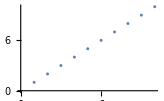
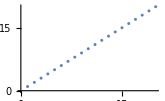
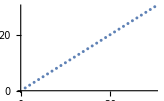

```mathematica
Table[ListPlot[Range[10*n]],{n,3}]
```

这里是由连续段数的饼状图组成的表：

```mathematica
Table[PieChart[Table[1,n]],{n,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

到目前为止，我们一直使用 n 作为我们的变量。这是一种很常用的选择。但实际上我们可以使用任何我们想要的(小写)字母，或者任何字母的组合。重要的是，无论变量出现在哪里，都使用一样的名称。

expt 就是一个非常好的变量名称：

```mathematica
Table[2^expt,{expt,10}]
```

{2,4,8,16,32,64,128,256,512,1024}

这里我们用 x 作为变量名，而它恰好出现了好几次：

```mathematica
Table[{x,x+1,x^2},{x,5}]
```

{{1,2,1},{2,3,4},{3,4,9},{4,5,16},{5,6,25}}

在 Table[f[n],{n,5}] 中，n 的值为 1、2、3、4、5。对于 Table[f[n],{n,3,5}] 来说，n 从 3 开始：3、4、5。

这将创建一个 n 从 1 到 10 的表：

```mathematica
Table[f[n],{n,10}]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

这将创建一个 n 从 4 到 10 的表：

```mathematica
Table[f[n],{n,4,10}]
```

{f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

这将创建一个 n 从 4 到 10，步长为 2 的表：

```mathematica
Table[f[n],{n,4,10,2}]
```

{f[4],f[6],f[8],f[10]}

Wolfram 语言强调一致性，因此，举例来说，Range 设置为处理初始值和结束值，就像 Table 一样。

生成从 4 到 10 的列表：

```mathematica
Range[4,10]
```

{4,5,6,7,8,9,10}

生成从 4 到 10，步长为 2 的列表：

```mathematica
Range[4,10,2]
```

{4,6,8,10}

从 0 到 1，步长为 0.1：

```mathematica
Range[0,1,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

在 Wolfram 语言中，通常有很多方法可以做同样的事情。例如，这里是 Table 和 Range 如何生成相同的绘图。

生成一个表并进行绘制：

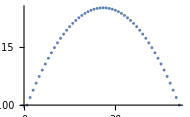

```mathematica
ListPlot[Table[x-x^2,{x,0,1,.02}]]
```

对数值范围进行算术运算，能得到同样的结果：

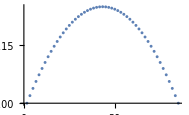

```mathematica
ListPlot[Range[0,1,.02]-Range[0,1,.02]^2]
```

Table 总是单独计算它生成的列表中的每一项，如果你在 Table 中使用 RandomInteger，你就可以看到这一点。

这将生成 20 个独立的随机整数，最大不超过 10：

```mathematica
Table[RandomInteger[10],20]
```

{3,1,4,3,6,7,6,10,9,2,1,4,5,8,3,8,3,8,3,0}

RandomInteger 实际上也可以直接生成列表。

这样也可以生成 20 个大小不超过 10 的随机整数：

```mathematica
RandomInteger[10,20]
```

{3,0,3,1,9,6,0,8,5,2,7,8,0,10,4,4,9,5,7,1}

词汇

Table[x,5] |   | 创建包含 5 个 x 副本的列表
Table[f[n],{n,10}] |   | 包含 f[n] 的值的列表，其中 n 最大为 10
Table[f[n],{n,2,10}] |   | 包含 f[n] 的值的列表，其中 n 为 2 到 10
Table[f[n],{n,2,10,4}] |   | 包含 f[n] 的值的列表，其中 n 为 2 到 10，步长为 4
Range[5,10] |   | 从 5 到 10 的数字列表
Range[10,20,2] |   | 从 10 到 20 的数字列表，步长为 2
RandomInteger[10,20] |   | 20 个 10 以内的随机数字的列表

"共有 10 道习题"
"以及 11 道附加题" | "开始练习 »"

创建一个将 1000 重复 5 次的列表。»

| 期望输出： |  
  | {1000,1000,1000,1000,1000} |

创建包含  n^3 的表，其中 n 为 10 到 20。»

| 期望输出： |  
  | {1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000} |

创建前 20 个数字的平方的数轴图。»

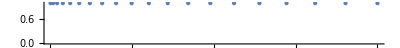
| 期望输出： |  
  | -Graphics- |

创建 20 以内的偶数(2, 4, 6, ...)的列表。»

| 期望输出： |  
  | {2,4,6,8,10,12,14,16,18,20} |

使用 Table 来创建与 Range[10] 相同的结果。»

| 期望输出： |  
  | {1,2,3,4,5,6,7,8,9,10} |

创建前 10 个数字的平方的条形图。»

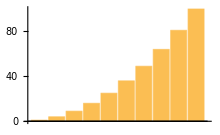
| 期望输出： |  
  | -Graphics- |

创建一个表，包含前 10 个数字的平方的各位数字。»

| 期望输出： |  
  | {{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}} |

将前 100 个数字的平方的位数绘制成线条图。»

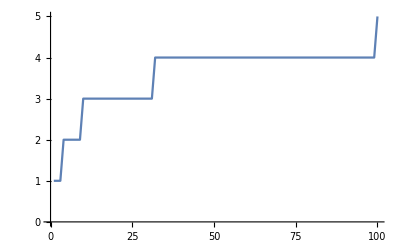
| 期望输出： |  
  | -Graphics- |

创建一个表，包含前 20 个数字的平方的首位数字。»

| 期望输出： |  
  | {1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4} |

将前 100 个数字的平方的首位数字绘制成线条图。»

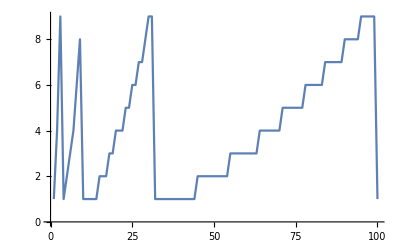
| 期望输出： |  
  | -Graphics- |

创建一个列表，包含  n^3 与 n^2 的差值，其中 n 最大为10。»

| 期望输出： |  
  | {0,4,18,48,100,180,294,448,648,900} |

创建 100 以内的奇数(1, 3, 5, ...)列表。»

| 期望输出： |  
  | {1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99} |

创建 100 以内的偶数的平方的列表。»

| 期望输出： |  
  | {4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000} |

使用 Range 来创建列表 {-3,-2,-1,0,1,2}。»

| 期望输出： |  
  | {-3,-2,-1,0,1,2} |

创建一个列表，其中的每个元素为由 n、n^2 以及 n^3 组成的列，n 最大为 20。»

| 期望输出： |  
  | {1
1
1,2
4
8,3
9
27,4
16
64,5
25
125,6
36
216,7
49
343,8
64
512,9
81
729,10
100
1000,11
121
1331,12
144
1728,13
169
2197,14
196
2744,15
225
3375,16
256
4096,17
289
4913,18
324
5832,19
361
6859,20
400
8000} |

绘制前 100 个数字的平方的最后一位数字的线条图。»

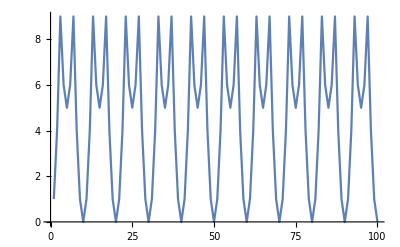
| 期望输出： |  
  | -Graphics- |

绘制前 100 个 3 的倍数的第一位数字的线条图。»

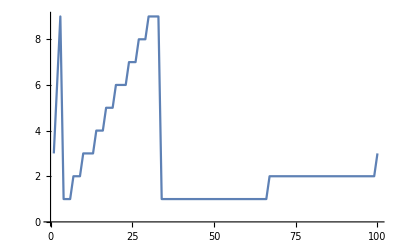
| 期望输出： |  
  | -Graphics- |

创建 200 以内的数字的各位数字之和的线条图。»

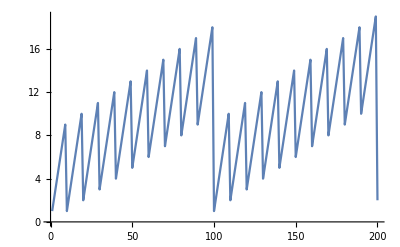
| 期望输出： |  
  | -Graphics- |

创建前 100 个数字的平方的各位数字之和的线条图。»

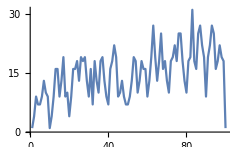
| 期望输出： |  
  | -Graphics- |

绘制数字  1/n  的数轴图，其中 n 从 1 到 20。»

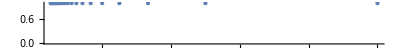
| 期望输出： |  
  | -Graphics- |

创建随机整数的线条图，其中第 n 个整数在 0 到 n 之间。»

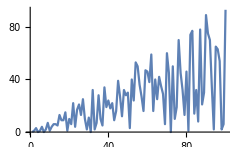
| 期望输出： |  
  | -Graphics- |

问&答

Table[n^2,{n,5}] 中的 {...} (列表)是什么意思？

列表总是用于将对象集合在一起的一种方式。这里它所收集的是变量 n 及其范围 5。在 Wolfram 语言中，这种对列表的使用被称为迭代器规范。

Table[n^2,{n,5}] 中为什么需要  {...} (列表)？

以便可以很容易地推广到多维数组，比如 Table[x^2-y^2,{x,5},{y,5}]。

对变量的名称有什么限制？

它们可以是任何字母或数字的组合，但不能以数字开头，并且也不应该以大写字母开头，以避免它们可能与 Wolfram 语言的内置功能相混淆。

如果名字向来都不重要，那为什么还非要给变量命名呢？

好问题！在第 26 节中，我们将看到如何避免使用命名的变量。它非常优雅，但比我们在这里用的 Table 要抽象一些。

Range 能处理负数吗？

可以。Range[-2,2] 将生成 {-2,-1,0,1,2}。Range[2,-2] 将生成 {}，但是 Range[2,-2,-1] 将生成 {2,1,0,-1,-2}.

技术笔记

如果你指定的步长与你给定的范围不相符，Range 和 Table 就会按步长走到最远，并可能会在上限前停止。(所以 Range[1,6,2] 将给出 {1,3,5}，在 5 而不是 6 时停止)

使用像 Table[x,20] 这样的形式至少需要 Wolfram 语言的 10.2 版本。在早期版本中，必须指定为  Table[x,{20}]。

探索更多

Wolfram 语言中的 Table 函数 »